# Two-loop onshell mass operator

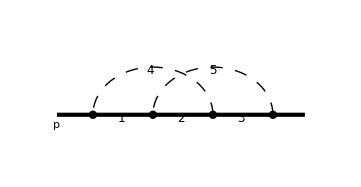

## Finding reduction rules

#### Initialization

```mathematica
<<LiteRed`(*Loading the package*)
SetDirectory[NotebookDirectory[]];(*Setting working directory*)
SetDim[d];(*d stands for the dimensionality*)
Declare[{l,r,p},Vector];(*vector variables*)
sp[p,p]=1;(*constraint*)
```

#### Defining the basis and searching for the symmetries & reduction rules

```mathematica
NewBasis[p2,{sp[p-l]-1,sp[p-l-r]-1,sp[p-r]-1,l,r},{l,r},Directory->"p2 dir"];(*Basis definition.*)
GenerateIBP[p2](*IBP generation. Can be also invoked by passing GenerateIBP->True option in NewBasis call*)
AnalyzeSectors[p2](*Zero and simple sectors determination. Can be also invoked by passing AnalyzeSectors->True option in NewBasis call.*)
FindSymmetries[p2](*Finding unique and mapped sectors. Can be also invoked by passing FindSymmetries->True option in NewBasis call.*)
SolvejSector/@UniqueSectors[p2]
```

```mathematica
DiskSave[p2];
```

## Attaching graph

```mathematica
AttachGraph[js[p2,1,1,1,1,1],{
{1->2,"1"},
{2->3,"1"},
{3->4,"1"},
{1->3,"0"},
{2->4,"0"},
{0->1,"p"},
{4->0,"p"}
}];(*Attach the graph to the highest sector. The graphs for the subsectors are determined automatically. The external legs should start/end at vertex number 0. The internal vertices should be positive integer. The order of the internal lines should correspond to the order of denominators in the sector.*)
(* In this example the number of vertices is 5 and, e.g. 1->2 denoted the edge from vertex 1 to vertex 2. We label massive/massless lines with "1"/"0", the external legs are labelled with "p"*)
```

```mathematica
SetOptions[GraphPlot,MultiedgeStyle->0.3,VertexRenderingFunction->({If[#2>0,Black,Blue],Disk[#1,0.03]}&),EdgeRenderingFunction->(Replace[#3,{
"1"->{Thick,Black,Line[#1]},
"0"->{Thin,Black,Dashed,Line[#1]},
"p"->{Thickness[0.01],Blue,Line[#1]},
_->Line[#1]
}]&)];(*Embellish the graph output by standard Mathematica means*)
```

Draw graphs for the master integrals

```mathematica
GraphPlot/@jGraph/@MIs[p2]
```

Draw graphs for the unique sectors

```mathematica
GraphPlot/@jGraph/@UniqueSectors[p2]
```

Draw graphs for nonzero sectors

```mathematica
GraphPlot/@jGraph/@NonZeroSectors[p2]
```

```mathematica
DiskSave[p2](*Saving.*)
Quit[](*Quitting the kernel*)
```

## Application

```mathematica
<<LiteRed`(*Loading the package*)
SetDirectory[NotebookDirectory[]];(*Setting working directory*)
SetDim[d];(*d stands for the dimensionality*)
Declare[{l,r,p},Vector];(*vector variables*)
sp[p,p]=1;(*constraint*)
```

```mathematica
<<"p2 dir/p2";
```

```mathematica
IBPReduce[j[p2,1,1,1,1,1]]
```

```mathematica
Quit[]
```